# B-Convergence

Presentation by Frederik Schnack

### Prothero & Robinson Example:

#### Details on the function:

```mathematica
(* Define parameters and the function (used by Seinfeld): *)
ψ[x_] = 10-(10+x)Exp[- x];
λ = -10; 
x0 = 0;
T = 1;
rhs[x_, y_]=λ(y-ψ[x])+ψ'[x];
system = {y'[x]== λ(y[x]-ψ[x])+ψ'[x] ,y[x0]==ψ[x0]};
```

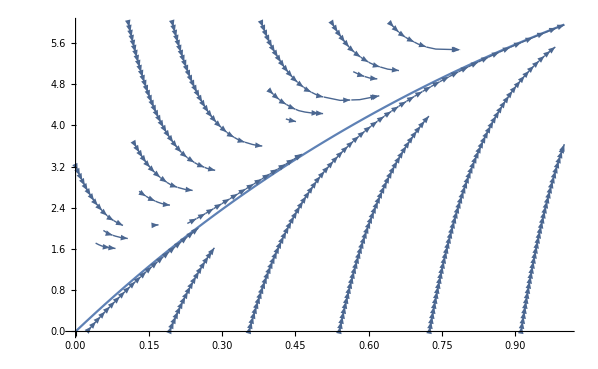

```mathematica
tr = StreamPlot[{1, rhs[x, y]},{x,x0,T},{y,0,6}];
sol = Plot[ψ[x], {x, x0, T}];
Show[sol, tr]
```

#### Methods applied:

```mathematica
?NDSolve`*Coefficients
```

```mathematica
(* Dahlquist Test Equation:
system = {y'[x]== λ y [x],y[x0]== 1};
φ[x_] = Exp[λ x];*)

(* Prothero & Robinson System: 
system = {y'[x]== λ(y[x]-φ[x])+φ'[x] ,y[x0]==φ[x0]};
φ[x_] =  -φ[x_] = 10-(10+x)Exp[- x];*)
```

```mathematica
gauss = List[];
radau1a = List[];
radau2a = List[];
lobattoa = List[];
lobattob = List[];
lobattoc = List[];

λ = -10^7;
x0 = 0;
T = 1;

φ[x_] = 10-(10+x)Exp[- x];
system = {y'[x]== λ(y[x]-φ[x])+φ'[x] ,y[x0]==φ[x0]};
p = 4;
startingstep = 0.1;
step = startingstep;
For[l=1, l<10, l++, 
sol1 = NDSolve[system,y,{x,x0,T},Method->{"FixedStep",Method->{"ImplicitRungeKutta", "Coefficients"-> "ImplicitRungeKuttaGaussCoefficients", "DifferenceOrder" -> p}}, StartingStepSize->step];
s1[x_]=(y[x]/.sol1);
gauss = Append[gauss, {step,Abs[(s1[T]-φ[T])[[1]]]}];

sol2 = NDSolve[system,y,{x,x0,T},Method->{"FixedStep",Method->{"ImplicitRungeKutta", "Coefficients"-> "ImplicitRungeKuttaRadauIACoefficients", "DifferenceOrder" -> p}}, StartingStepSize->step];
s2[x_]=(y[x]/.sol2);
radau1a = Append[radau1a, {step,Abs[(s2[T]-φ[T])[[1]]]}];

sol3 = NDSolve[system,y,{x,x0,T},Method->{"FixedStep",Method->{"ImplicitRungeKutta", "Coefficients"-> "ImplicitRungeKuttaRadauIIACoefficients", "DifferenceOrder" ->p}}, StartingStepSize->step];
s3[x_]=(y[x]/.sol3);
radau2a = Append[radau2a, {step,Abs[(s3[T]-φ[T])[[1]]]}];

sol4 = NDSolve[system,y,{x,x0,T},Method->{"FixedStep",Method->{"ImplicitRungeKutta", "Coefficients"-> "ImplicitRungeKuttaLobattoIIIACoefficients", "DifferenceOrder" -> p}}, StartingStepSize->step];
s4[x_]=(y[x]/.sol4);
lobattoa = Append[lobattoa, {step,Abs[(s4[T]-φ[T])[[1]]]}];

sol5 = NDSolve[system,y,{x,x0,T},Method->{"FixedStep",Method->{"ImplicitRungeKutta", "Coefficients"-> "ImplicitRungeKuttaLobattoIIIBCoefficients", "DifferenceOrder" -> p}}, StartingStepSize->step];
s5[x_]=(y[x]/.sol5);
lobattob = Append[lobattob, {step,Abs[(s5[T]-φ[T])[[1]]]}];

sol6 = NDSolve[system,y,{x,x0,T},Method->{"FixedStep",Method->{"ImplicitRungeKutta", "Coefficients"-> "ImplicitRungeKuttaLobattoIIICCoefficients", "DifferenceOrder" -> p}}, StartingStepSize->step];
s6[x_]=(y[x]/.sol6);
lobattoc = Append[lobattoc, {step,Abs[(s6[T]-dieφ[T])[[1]]]}];

step =  startingstep*2^(-l)
]
```

NDSolve`ImplicitRungeKutta::cmsing: Singular coefficient matrix encountered for NDSolve`ImplicitRungeKuttaLobattoIIIACoefficients, which is not suitable for stiff systems.

NDSolve`ImplicitRungeKutta::cmsing: Singular coefficient matrix encountered for NDSolve`ImplicitRungeKuttaLobattoIIIBCoefficients, which is not suitable for stiff systems.

NDSolve`ImplicitRungeKutta::cmsing: Singular coefficient matrix encountered for NDSolve`ImplicitRungeKuttaLobattoIIIACoefficients, which is not suitable for stiff systems.

General::stop: Further output of NDSolve`ImplicitRungeKutta::cmsing will be suppressed during this calculation.

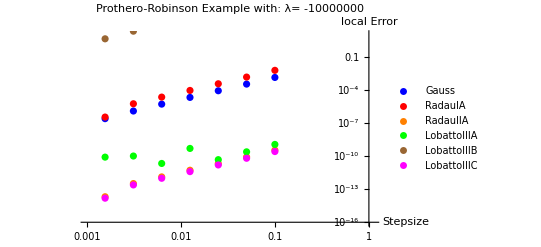

```mathematica
gp = ListLogLogPlot[gauss, PlotStyle-> Blue, PlotLegends -> {"Gauss"}];
rp1 = ListLogLogPlot[radau1a, PlotStyle-> Red, PlotLegends -> {"RadauIA"}];
rp2 = ListLogLogPlot[radau2a, PlotStyle-> Orange, PlotLegends -> {"RadauIIA"}];
lba = ListLogLogPlot[lobattoa, PlotStyle-> Green, PlotLegends -> {"LobattoIIIA"}];
lbb = ListLogLogPlot[lobattob, PlotStyle-> Brown, PlotLegends -> {"LobattoIIIB"}];
lbc = ListLogLogPlot[lobattoc, PlotStyle-> Magenta, PlotLegends -> {"LobattoIIIC"}];
Show[gp,rp1, rp2, lba, lbb, lbc, PlotRange ->{{Log[0.001], 0.1},{Log[10^-16], Log[10]}}, PlotLabel -> StringForm["Prothero-Robinson Example with: λ= ``", ScientificForm[λ,1]], AxesLabel-> {"Stepsize",  "local Error"}, AxesOrigin -> {0, Log[10 ^-16]}]
```

#### Proof of the error estimate:

```mathematica
Series[φ[x0+c[i]h],{h,0,4}]-Series[φ[x0]+h ∑_(j=1)^s a[i,j] φ'[x0+h c[j]]/.s-> 2,{h,0,4}] //FullSimplify
```

-(a[i,1]+a[i,2]-c[i]) φ'[0] h+1/2 (-2 a[i,1] c[1]-2 a[i,2] c[2]+c[i]^2) φ''[0] h^2+1/6 (-3 a[i,1] c[1]^2-3 a[i,2] c[2]^2+c[i]^3) φ^(3)[0] h^3+1/24 (-4 a[i,1] c[1]^3-4 a[i,2] c[2]^3+c[i]^4) φ^(4)[0] h^4+O[h]^5

```mathematica
Series[φ[x0+h],{h,0,4}] -Series[φ[x0]+h ∑_(j=1)^s b[j] φ'[x0+h c[j]]/. s-> 2,{h,0,4}]//FullSimplify
```

-(-1+b[1]+b[2]) φ'[0] h-1/2 ((-1+2 b[1] c[1]+2 b[2] c[2]) φ''[0]) h^2-1/6 ((-1+3 b[1] c[1]^2+3 b[2] c[2]^2) φ^(3)[0]) h^3-1/24 ((-1+4 b[1] c[1]^3+4 b[2] c[2]^3) φ^(4)[0]) h^4+O[h]^5

```mathematica
ReleaseHold[Hold[SolveAlways[Series[φ[x0+h],{h,0,n}]==
Series[φ[x0]+h ∑_(j=1)^s b[j] φ'[x0+h c[j]]/.s->2,{h,0,n}],
Append[Table[Derivative[k][φ][x0],{k,0,n}],h]]]/.n->4]
```

{{b[1]→1/2,b[2]→1/2,c[1]→1/6 (3-√3),c[2]→1/6 (3+√3)},{b[1]→1/2,b[2]→1/2,c[1]→1/6 (3+√3),c[2]→1/6 (3-√3)}}

### Proof of the local Error-Estimate:

```mathematica
Series[y[x0 + c[i]h],{h,0,4}]-Series[y [xo]+h ∑_(j=1)^s a[i,j] y'[x0+h c[j]]/.s->3,{h,0,4}]//FullSimplify
```

(y[0]-y[xo])-(a[i,1]+a[i,2]+a[i,3]-c[i]) y'[0] h+1/2 (-2 (a[i,1] c[1]+a[i,2] c[2]+a[i,3] c[3])+c[i]^2) y''[0] h^2+1/6 (-3 (a[i,1] c[1]^2+a[i,2] c[2]^2+a[i,3] c[3]^2)+c[i]^3) y^(3)[0] h^3+1/24 (-4 (a[i,1] c[1]^3+a[i,2] c[2]^3+a[i,3] c[3]^3)+c[i]^4) y^(4)[0] h^4+O[h]^5

```mathematica
Series[y[x0 + h],{h,0,3}]-Series[y [xo]+h ∑_(j=1)^s b[j] y'[x0+h c[j]]/.s->3,{h,0,4}]//FullSimplify
```

(y[0]-y[xo])-(-1+b[1]+b[2]+b[3]) y'[0] h-1/2 ((-1+2 b[1] c[1]+2 b[2] c[2]+2 b[3] c[3]) y''[0]) h^2-1/6 ((-1+3 b[1] c[1]^2+3 b[2] c[2]^2+3 b[3] c[3]^2) y^(3)[0]) h^3+O[h]^4